# Bessel and Related Function

## Graphs, integration, differentiation

```mathematica
x^2 D[y[x], x,x]+x D[y[x], x]+(x^2-α^2)y[x]==0
```

This comes from the radial part of Laplaian equation in cylindrical coordinate

## Bessel Function of First Kind

```mathematica
Series[BesselJ[1,x],{x,0,10}]
```

x/2-x^3/16+x^5/384-x^7/18432+x^9/1474560+O[x]^11

```mathematica
BJ[α_,x_,n_]:=Sum[ (-1)^m/(m! Gamma[m+α+1])(x/2)^(2m+α),{m,0,n}]
```

```mathematica
BJ[1,x,9]
```

x/2-x^3/16+x^5/384-x^7/18432+x^9/1474560-x^11/176947200+x^13/29727129600-x^15/6658877030400+x^17/1917756584755200-x^19/690392370511872000

```mathematica
Integrate[(-1)^m/(m! Gamma[m+α+1])(x/2)^(2m+α),x]
```

((-1)^m 2^(-2 m-α) x^(1+2 m+α))/((1+2 m+α) m! Gamma[1+m+α])

```mathematica
InBJ[α_,x_,n_]:=Sum[ ((-1)^m x)/((1+2 m+α) m! Gamma[1+m+α])(x/2)^(2m+α),{m,0,n}]
```

```mathematica
InBJ[1,x,9]
```

x^2/4-x^4/64+x^6/2304-x^8/147456+x^10/14745600-x^12/2123366400+x^14/416179814400-x^16/106542032486400+x^18/34519618525593600-x^20/13807847410237440000

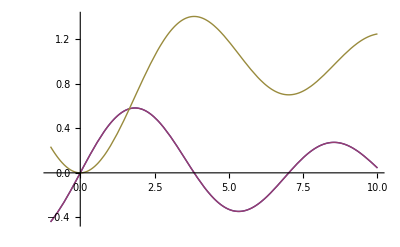

```mathematica
Plot[{BesselJ[1,x],BJ[1,x,14],InBJ[1,x,16]},{x,-1,10}]
```

```mathematica
BesselJ[1,x+ⅈ y]
```

BesselJ[1,x+ⅈ y]

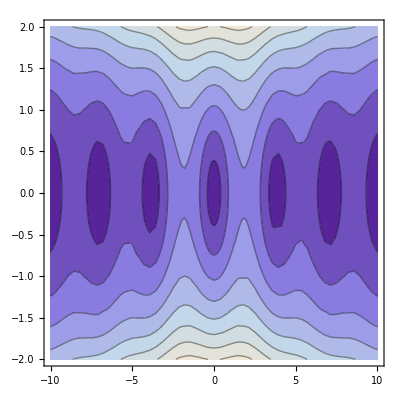

```mathematica
ContourPlot[Norm[BesselJ[1,x+ⅈ y]],{x,-10,10},{y,-2,2}]
```

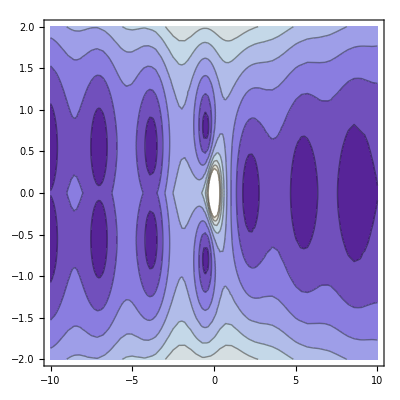

```mathematica
ContourPlot[Norm[BesselY[1,x+ⅈ y]],{x,-10,10},{y,-2,2}]
```